```mathematica
Quit
```

### 3D Coordinates

```mathematica
Manipulate[
Which[
type==1,
Show[{
Graphics3D[{Blue,Thick,Line[{{a,0,0},{a,b,0}}],Red,Line[{{0,b,0},{a,b,0}}],Darker@Green,Line[{{a,b,0},{a,b,c}}],
Darker@Gray,Arrow[{{-6,0,0},{6,0,0}}],Arrow[{{0,-6,0},{0,6,0}}],Arrow[{{0,0,-6},{0,0,6}}]},
ImageSize->400{1,1},Ticks->None,Axes->False,Boxed->False,AxesOrigin->{0,0,0},PlotRange->{{-6,6},{-6,6},{-6,6}},AxesStyle->Gray,AspectRatio->1,ViewPoint->{Pi,2π/5,Pi/2},ViewVertical->{0,0,1}],
Graphics3D[{{Opacity[.1],EdgeForm[LightGray],FaceForm[Red,Green],Cuboid[{0,0,0},{a,b,c}]},Black,Sphere[{a,b,c},.1],Style[Text[Row[{"(",Style["x",Italic], ", ",Style["y",Italic], ", ",Style["z",Italic],")"}],{a,b+1.25,c+.65}],16,Italic,Black],Style[Text["x",{0.5a,b+0.5,0}],16,Red,Italic],Style[Text["x",{5,.75,0}],25,Darker@Gray,Italic],
Style[Text["y",{a-.65,b/2,0.2}],16,Blue,Italic],Style[Text["y",{0,5.5,-0.5}],25,Darker@Gray,Italic],
Style[Text["z",{a+1,b+0.7,0.8c}],16,Darker@Green,Italic],Style[Text["z",{0,0.7,5.5}],25,Darker@Gray,Italic],
 {Magenta,Thick,Arrow[{{a,b,c},{a+3,b,c}}]},
 Style[Text["(ⅇ⃗)_x",{a+3,b-0.35,c+0.65}],22,Magenta,Bold],
{Magenta,Thick,Arrow[{{a,b,c},{a,b+2,c}}]},
 Style[Text["(ⅇ⃗)_y",{a,b+2.5,c}],22,Magenta,Bold],
{Magenta,Thick,Arrow[{{a,b,c},{a,b,c+2.5}}]},
 Style[Text["(ⅇ⃗)_z",{a,b+0.5,c+2.5}],22,Magenta,Bold]
}]
}],
type==2,
Show[{
ParametricPlot3D[{(ρ/3)*Cos[π*t],(ρ/3)*Sin[π*t],0},{t,0,If[ϕ==0,.0001,ϕ/π]},PlotStyle->Directive[Blue,Thick],PlotRange->{{-5,5},{-5,5},{-5,5}},ImageSize->400{1,1},Mesh->None,PerformanceGoal->"Quality",Ticks->None,Axes->True,AxesStyle->Gray,Boxed->False,AxesOrigin->{0,0,0},AspectRatio->1,ViewPoint->{Pi,2π/5,Pi/2},ViewVertical->{0,0,1}],
ParametricPlot3D[{t*Cos[ϕ],t*Sin[ϕ],0},{t,0,ρ},PlotStyle->Directive[Red,Thick]],
ParametricPlot3D[{ρ*Cos[ϕ],ρ*Sin[ϕ],k},{k,0,z},PlotStyle->Directive[Darker@Green,Thick]],
ParametricPlot3D[{ρ*Cos[p],ρ*Sin[p],z},{p,0π,2π},PlotStyle->Directive[Thick,Darker@Green]],
ParametricPlot3D[{t*Cos[ϕ],t*Sin[ϕ],z},{t,0,ρ},PlotStyle->Directive[Red,Thick,Dashed]],
Graphics3D[{{Opacity[.3],EdgeForm[LightGray],FaceForm[Yellow,Green],Cylinder[{{0,0,0},{0,0,z}},ρ]},Black,Sphere[{ρ*Cos[ϕ],ρ*Sin[ϕ],z},.1],
Darker@Gray,Arrow[{{-5,0,0},{5,0,0}}],Arrow[{{0,-5,0},{0,5,0}}],Arrow[{{0,0,-5},{0,0,5}}],
Style[Text[Row[{"(",Style["ρ"],", ϕ, ",Style["z",Italic],")"}],{(ρ+1)*Cos[ϕ],(ρ+0.3)*Sin[ϕ]-1,z}],16,Black],Style[Text["ϕ",{(ρ/2)*Cos[ϕ/2],(ρ/2)*Sin[ϕ/2],-0.15}],16,Blue],
Style[Text["ρ",{(ρ-1)*Cos[1.05ϕ],(ρ-1)*Sin[1.05ϕ],.5}],16,Red],Style[Text["z",{(ρ+.8)*Cos[ϕ],(ρ+0.75)*Sin[ϕ],3z/4}],16,Darker@Green,Italic],
 Style[Text["x",{5,.5,0}],25,Darker@Gray,Italic],Style[Text["y",{0,5,1}],25,Darker@Gray,Italic],
 Style[Text["z",{.5,0,5+0.5}],25,Darker@Gray,Italic],
 {Magenta,Thick,Arrow[{{ρ* Cos[ϕ],ρ*Sin[ϕ],z},{(ρ+2.5)*Cos[ϕ],(ρ+2.5)*Sin[ϕ],z}}]},
 Style[Text["(ⅇ⃗)_ρ",{(ρ+2.5)*Cos[ϕ],(ρ+2.5)*Sin[ϕ]+0.35,z+0.35}],22,Magenta,Bold],
{Magenta,Thick,Arrow[{{ρ* Cos[ϕ],ρ*Sin[ϕ],z},{ρ*Cos[ϕ]-1.75Sin[ϕ],ρ*Sin[ϕ]+1.75*Cos[ϕ],z}}]},
 Style[Text["(ⅇ⃗)_ϕ",{ρ*Cos[ϕ]-1.75Sin[ϕ],ρ*Sin[ϕ]+1.75*Cos[ϕ]+0.5,z}],22,Magenta,Bold],
{Magenta,Thick,Arrow[{{ρ* Cos[ϕ],ρ*Sin[ϕ],z},{ρ*Cos[ϕ],ρ*Sin[ϕ],z+1.5}}]},
 Style[Text["(ⅇ⃗)_z",{ρ*Cos[ϕ],ρ*Sin[ϕ]+0.5,z+1.5}],22,Magenta,Bold]
}]
}],
type==3,
Show[{
ParametricPlot3D[{ρ*Sin[θ]*Cos[ϕ],ρ*Sin[θ]*Sin[ϕ],ρ*Cos[θ]},{ρ,0,r},PlotStyle->Directive[Thick,Red],PlotRange->{{-5,5},{-5,5},{-5,5}},ImageSize->400{1,1},Mesh->None,Ticks->None,Axes->False,AxesStyle->Gray,Boxed->False,AxesOrigin->{0,0,0},AspectRatio->1,PerformanceGoal->"Quality",ViewPoint->{Pi,2π/5,Pi/3},ViewVertical->{0,0,1}],
ParametricPlot3D[{r/4*Sin[p]*Cos[ϕ],r/4*Sin[p]*Sin[ϕ],r/4*Cos[p]},{p,0,θ},PlotStyle->Directive[Thick,Darker@Green]],
ParametricPlot3D[{r*Sin[p]*Cos[ϕ],r*Sin[p]*Sin[ϕ],r*Cos[p]},{p,0.05,0.85π},PlotStyle->Directive[Thick,Darker@Green]],
ParametricPlot3D[{r*Sin[p]*Cos[ϕ],r*Sin[p]*Sin[ϕ],r*Cos[p]},{p,0.85π,2.05π},PlotStyle->Directive[Thick,Darker@Green,Dashed]],
ParametricPlot3D[{r*Sin[θ]*Cos[p],r*Sin[θ]*Sin[p],r*Cos[θ]},{p,-0.35π,0.7π},PlotStyle->Directive[Thick,Darker@Green]],
ParametricPlot3D[{r*Sin[θ]*Cos[p],r*Sin[θ]*Sin[p],r*Cos[θ]},{p,0.7π,1.65π},PlotStyle->Directive[Thick,Darker@Green,Dashed]],
ParametricPlot3D[{r/4*Sin[π/2]*Cos[t],r/4*Sin[π/2]*Sin[t],r/4*Cos[π/2]},{t,0,ϕ},PlotStyle->Directive[Thick,Blue]],
Graphics3D[{{Opacity[.1],FaceForm[Green,Blue],Sphere[{{0,0,0}},r]},
Black,Sphere[{r*Sin[θ]*Cos[ϕ],r*Sin[θ]*Sin[ϕ],r*Cos[θ]},.1],
Darker@Gray,Arrow[{{-5,0,0},{5,0,0}}],Arrow[{{0,-5,0},{0,5,0}}],Arrow[{{0,0,-5},{0,0,5}}],
{Blue,Thick,Line[{{0,0,0},{r Sin[θ]*Cos[ϕ],r*Sin[θ]*Sin[ϕ],0}}],
Dashed,Line[{{r Sin[θ]*Cos[ϕ],r*Sin[θ]*Sin[ϕ],r*Cos[θ]},{r Sin[θ]*Cos[ϕ],r*Sin[θ]*Sin[ϕ],0}}]},
Style[Text[Row[{"(",Style["r",Italic],", θ, ϕ)"}],{(r)*Sin[(θ+.2)]*Cos[ϕ],(r+1)*Sin[(θ+.2)]*Sin[ϕ]+0.25,(r+1)*Cos[(θ+.2)]-0.2}],16,Black],
Style[Text[Style["r",Italic,Bold],{r/3*Sin[(θ+.25)]*Cos[ϕ],r/3*Sin[(θ+.25)]*Sin[ϕ]+0.35,r*Cos[(θ+.25)+0.2]}],16,Red],
              Style[Text["θ",{(r/3)*Sin[θ/2]*Cos[ϕ],(r/3)*Sin[θ/2]*Sin[ϕ]+0.1,(r/2)*Cos[θ/2]-0.35}],16,Darker@Green],
              Style[Text["ϕ",{(r/2.25)*Sin[π/2]*Cos[ϕ/2],(r/2)*Sin[π/2]*Sin[ϕ/2],-0.2}],16,Blue],
 Style[Text["x",{5,.5,0}],25,Darker@Gray,Italic],Style[Text["y",{0.5,5,0}],25,Darker@Gray,Italic],
 Style[Text["z",{.5,0,5+0.5}],25,Darker@Gray,Italic],
 {Magenta,Thick,Arrow[{{r*Sin[θ]*Cos[ϕ],r*Sin[θ]*Sin[ϕ],r*Cos[θ]},{(r+2.5)*Sin[θ]*Cos[ϕ],(r+2.5)*Sin[θ]*Sin[ϕ],(r+2.5)*Cos[θ]}}]},
 Style[Text["(ⅇ⃗)_r",{(r+2.5)*Sin[θ]*Cos[ϕ],(r+2.5)*Sin[θ]*Sin[ϕ],(r+2.5)*Cos[θ]+0.3}],22,Magenta,Bold],
{Magenta,Thick,Arrow[{{r*Sin[θ]*Cos[ϕ],r*Sin[θ]*Sin[ϕ],r*Cos[θ]},{r*Sin[θ]*Cos[ϕ]+2Cos[θ]*Cos[ϕ],r*Sin[θ]*Sin[ϕ]+2Cos[θ]*Sin[ϕ],r*Cos[θ]-2*Sin[θ]}}]},
 Style[Text["(ⅇ⃗)_θ",{r*Sin[θ]*Cos[ϕ]+2Cos[θ]*Cos[ϕ],r*Sin[θ]*Sin[ϕ]+2Cos[θ]*Sin[ϕ]+0.5,r*Cos[θ]-2*Sin[θ]}],22,Magenta,Bold],
{Magenta,Thick,Arrow[{{r*Sin[θ]*Cos[ϕ],r*Sin[θ]*Sin[ϕ],r*Cos[θ]},{r*Sin[θ]*Cos[ϕ]-2Sin[ϕ],r*Sin[θ]*Sin[ϕ]+2Cos[ϕ],r*Cos[θ]}}]},
Style[Text["(ⅇ⃗)_ϕ",{r*Sin[θ]*Cos[ϕ]-2Sin[ϕ],r*Sin[θ]*Sin[ϕ]+2Cos[ϕ]+0.5,r*Cos[θ]+0.5}],22,Magenta,Bold]
  }]
}]],
{{type,1,"coordinate system"},{1->"rectangular",2->"cylindrical",3->"spherical"},ControlPlacement->Top},
OpenerView[{"rectangular",Column[{
Control[{{a,3,Style["x",Italic]},-4,4,.2,Appearance->"Labeled",ImageSize->Tiny}],
Control[{{b,4,Style["y",Italic]},-4,4,.2,Appearance->"Labeled",ImageSize->Tiny}],
Control[{{c,3,Style["z",Italic]},-4,4,.2,Appearance->"Labeled",ImageSize->Tiny}],Spacer[150]
}]},Dynamic[If[type==1,True,False]],Enabled->False],
OpenerView[{"cylindrical",Column[{
Control[{{ρ,3},.01,4,Appearance->"Labeled",ImageSize->Tiny}],
Control[{{ϕ,π/4},0,2π,π/100,Appearance->"Labeled",ImageSize->Tiny}],
Control[{{z,3},-4.9,4.9,.2,Appearance->"Labeled",ImageSize->Tiny}],Spacer[150]
}]},Dynamic[If[type==2,True,False]],Enabled->False],
OpenerView[{"spherical",Column[{
Control[{{r,4},.01,5,Appearance->"Labeled",ImageSize->Tiny}],
Control[{{θ,π/4,"θ"},π/100,2π,π/100,Appearance->"Labeled",ImageSize->Tiny}],
Control[{{ϕ,π/3,"ϕ"},π/100,2π,π/100,Appearance->"Labeled",ImageSize->Tiny}],Spacer[150]
}]},Dynamic[If[type==3,True,False]],Enabled->False],
ControlPlacement->Left,
AutorunSequencing->{1}]
```

### curved-coordinates

```mathematica
Clear[a,b,g,label,PlotEulerAngles]
style={FontFamily->Times,Italic,FontSize->30};

PlotEulerAngles[a_,b_,g_,label_]:=
Module[{x1,y1,z1,x2,y2,z2,xp,yp,zp,arc1,arc2,arc3,arc1a,arc2a,arc3a},

(* Start with z rotation of angle alpha=a to get Subscript[x, 1], Subscript[y, 1], Subscript[z, 1]*)
x1 = RotationMatrix[a,{0,0,1}].{1,0,0};
y1= RotationMatrix[a,{0,0,1}].{0,1,0};
z1= RotationMatrix[a,{0,0,1}].{0,0,1};
(* then Subscript[y, 1] rotation  of angle beta=b to get Subscript[x, 2], Subscript[y, 2], Subscript[z, 2]*)
x2 =RotationMatrix[b,y1].x1;
y2 =RotationMatrix[b,y1].y1;
z2 =RotationMatrix[b,y1].z1;
(* finally Subscript[z, 2] rotation  of angle gamm=g to get x', y', z'*)
xp = RotationMatrix[g,z2].x2;
yp = RotationMatrix[g,z2].y2;
zp = RotationMatrix[g,z2].z2;

arc1 = Table[0.7RotationMatrix[tx,{0,0,1}].{0,1,0},{tx,-0.5,2,0.05}];
arc2 = Table[0.7RotationMatrix[tx,z2].y2,{tx,-1.5,1,0.05}];
arc3 = Table[0.7RotationMatrix[tx,-x1].z1,{tx,3.5,0,-0.05}];

arc1a = Table[0.7RotationMatrix[tx,{0,0,1}].{0,1,0},{tx,0.7,1.1,0.05}];
arc2a = Table[0.7RotationMatrix[tx,z2].y2,{tx,0,0.4,0.05}];
arc3a = Table[0.7RotationMatrix[tx,-x1].z1,{tx,1.55,1.2,-0.05}];
ps={-0.16,0.05,-0.19};
op=0.8;

Show[   


Graphics3D[{Opacity[op],RGBColor[0.1,1,0.1],Tube[arc2,0.01]}], Graphics3D[{Opacity[op],RGBColor[0.1,1,0.1],Arrow[Tube[arc2a,0.015]]}],
Graphics3D[{Opacity[op],RGBColor[0,0,1],Tube[arc3,0.01]}], Graphics3D[{Opacity[op],RGBColor[0,0,1],Arrow[Tube[arc3a,0.015]]}],
Graphics3D[{Opacity[op],RGBColor[1,0.3,0.3],Tube[arc1,0.01]}], Graphics3D[{Opacity[op],RGBColor[1,0.3,0.3],Arrow[Tube[arc1a,0.015]]}],
Graphics3D[{(*GrayLevel[.55],Specularity[White,30],*)Red,Sphere[ps,0.05]}(*,Lighting->Automatic*)],

Graphics3D[{
Text[Style["(q̂)_1",Red,Bold,FontSize->18],{-0.85,0.65,0.04}],
Text[Style["(q̂)_2",RGBColor[0.,0.85,0.],Bold,FontSize->18],{-0.1,-0.41,0.025}],
Text[Style["(q̂)_3",Blue,Bold,FontSize->18],{0,.1,0.05}],
Text[Style["P(q_1,q_2,q_3)",Black,Italic,FontSize->17],{-0.65,-0.2,-0.5}]}],



PlotRange->{{-.7,.7},{-.9,0.9},{-.7,.7}}, Boxed->False,Axes->False,
ViewAngle->0.55,ViewPoint->{-1.55,2.45,0.85},ViewVertical->{-0.15,0.2,1},
ImageSize->{280,280}, SphericalRegion-> True]];

gg=PlotEulerAngles[0.7,0.5,1,True]
```

-Graphics3D-

### 3D curve

```mathematica
g1=ParametricPlot[{(3+Cos[5u])Cos[.7u],(3+Cos[8u]).7Sin[.7u]},{u,π/2,0.81π},PlotStyle->Cyan,
PlotRange->{{-0.5,1.2},All},Axes->True];
g2=ParametricPlot[{(3+Cos[5u])Cos[.7u],(3+Cos[8u]).7Sin[.7u]},{u,0.745π,0.81π},PlotStyle->Red,
PlotRange->{{-0.5,1.2},All},Axes->True];
g3=ParametricPlot[{(3+Cos[5u])Cos[.7u],(3+Cos[8u]).7Sin[.7u]},{u,0.72π,0.75π},PlotStyle->Blue,
PlotRange->{{-0.5,1.2},All},Axes->True];

Show[g1,g2,g3,PlotRange->{{-0.9,1.2},{1.4,2.8}},AxesOrigin->{0,1.5},Axes->False]
```

### 空间曲线若干定义

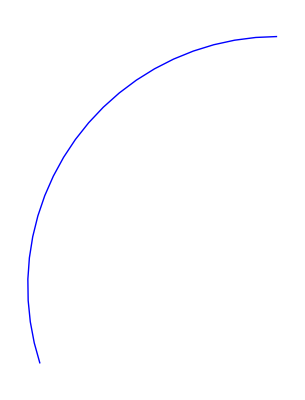

```mathematica
Graphics[{Blue,Thick,Circle[{0,0},1,{π/2,2.2π/2}]}]
```

### 角度变化动态图

```mathematica
Quit
```

```mathematica
x1=-1
x2=1;
y1=1/2;
y2=1/2;
fy[x_]:=x^2/2;
yp[x_]:=x;

Manipulate[

 Plot[fy[x],{x,-2,2},
                   Epilog->{PointSize[0.04],Point[{x1,y1}],Point[{x2,y2}],
                                    Text[Style[A,Italic,15],{x1-0.25,y1-0.1}],Text[Style[B,Italic,15],{x2+0.25,y1-0.1}],
                                    Red,Point[pt={x1+dx,fy[x1+dx]}],Arrow[{pt,pt+{ax=1/(√(yp[x1+dx]^2+1)),ay=ax yp[x1+dx]}}],
                                     Text[Style["τ⃗",Bold,18],pt+{ax+0.2,ay}]},
                  PlotRange->{{2x1,2x2},{-1,2}},PlotStyle->{Blue,Thick},AspectRatio->(3/2)/(x2-x1), ImageSize->{200,200}],
{{dx,0.0001},0.0001,2,0.001,AnimationRepetitions->3},SaveDefinitions->True]
```

-1

### 伽利略变换

-Graphics-

### 圆渐开线

#### 静态图

```mathematica
Show[ParametricPlot[{Cos[θ]+θ Sin[θ],Sin[θ]-θ Cos[θ]},{θ,0,π},PlotStyle->Blue],
Graphics[{Circle[{0,0},1],Thick,Red,Circle[{0,0},1,{1.5Pi/4,2Pi}]}],PlotRange->All,AxesOrigin->{0,0},Ticks->None,AxesLabel->None]
```

#### 动态图

```mathematica
Quit
```

```mathematica
Manipulate[
Show[
ParametricPlot[{Cos[u]+u Sin[u],Sin[u]-u Cos[u]},{u,0,θ},PlotStyle->Blue,PlotRange->7,Ticks->None],
Graphics[{Circle[{0,0},1],Thick,Red,Circle[{0,0},1,{θ,2Pi}],Line[{pt1={Cos[θ], Sin[θ]},pt2={Cos[θ]+θ Sin[θ],Sin[θ]-θ Cos[θ]}}],
Darker@Green,Circle[{0,0},0.25,{0,θ}],Line[{{0,0},{Cos[θ], Sin[θ]}}],Arrow[{pt2,pt3=pt2-1/Norm[pt2-pt1]{pt2[[2]]-pt1[[2]],pt1[[1]]-pt2[[1]]}}],
Text[Style["θ",12],{Cos[θ/2], Sin[θ/2]}/2],Text[Style["v⃗",16],pt2-1.5/Norm[pt2-pt1]{pt2[[2]]-pt1[[2]],pt1[[1]]-pt2[[1]]}],
PointSize[.019],{Red,Point[pt2]}
}]
  ],{{θ,0.002},0,2π,0.002}]
```

### 圆环

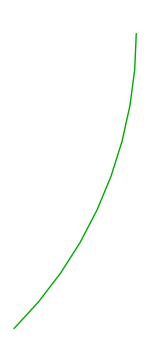

```mathematica
Graphics[{Darker@Green,Thick,Circle[{0,0},1,{315Degree,2π}]},ImageSize->150,PlotRange->1.5]
```

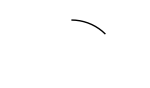

```mathematica
Graphics[{(*Darker@Green,*)Thick,Circle[{0,0},1,{π/4,π/2}]},ImageSize->150,PlotRange->{{-1.2,1.35},{-0.25,1.25}}]
```

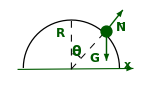

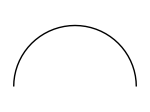

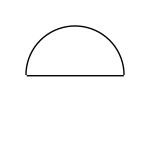

.

### spherical bowl

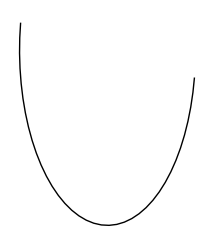

```mathematica
Graphics[Circle[{0,0},{0.5,1},{0.95π,2π-0.05π}]]
```

```mathematica
h=0.5;
Graphics[{RGBColor[0,0.5,0],Circle[{0,0},1,{π,2π}],Circle[{0,0},{1,0.25},{0,2π}],
{Dashed,Circle[{0,-h},0.98{√(1-h^2),0.25 √(1-h^2)},{0,π}]},Circle[{0,-h},0.98{√(1-h^2),0.25 √(1-h^2)},{π,2π}],
{Dashed,Circle[{0,0},{0.5,1},{0.93π,1.5π-0.0375π}]},Circle[{0,0},{0.5,1},{1.5π-0.0375π,2π-0.075π}],Darker@Gray,
Arrowheads[0.05],Arrow[{{-1.3,0},{1.4,0}}],Arrow[{{0,-1.3},{0,.7}}],Arrow[{{0.6,0.6},{-0.9,-0.9}}]},
ImageSize->200,PlotRange->{{-1.5,1.75},{-1.5,0.75}}]
```

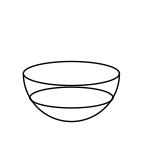

### sphere rolling in bowl

```mathematica
r0=0.25;
θ0=300 Degree;
tble=Table[{r0 Cos[u],r0 Sin[u]},{u,270Degree,θ0,1 Degree}];
pos={1.35r0 Cos[285Degree],1.35r0 Sin[285Degree]};
Graphics[{{Thickness[0.02],Cyan,Circle[{0,0},1,{π,2π}]},{Dashing[{0.03,0.015}],Circle[{0,0},r1=0.9,{3.8π/3,5.2π/3}],
Line[{{-1,0},{1,0}}],Line[{{0,0},{0,-1}}],Line[{{0,0},{r1 Cos[θ0],r1 Sin[θ0]}}]},
Arrowheads[.03],Arrow[tble],Text[Style["θ",18],pos]},
  PlotRange->{{-1.02,1.02},{-1.02,0.02}}]
```

### pending rope

#### 静态图

#### 动态图

```mathematica
Quit
```

```mathematica
p0={0,0};
Manipulate[
xb=pb[[1]];
yb=pb[[2]];
lb=Norm[pb];
eqset={c1 Cosh[c2/c1]+c3,yb-c1 Cosh[(xb-c2)/c1]-c3,l0-c1 Sinh[(xb-c2)/c1]-c1 Sinh[c2/c1]};
sol=FindRoot[eqset==0,{{c1,0.2},{c2,1},{c3,1.5}}];
shape=(c1 Cosh[(x-c2)/c1]+c3)/.sol;
If[0<l0-lb<10^-5,shape=yb/xb x];
g1=Plot[shape,{x,0,xb},PlotStyle->{Thick,Blue},PlotRange->{{-0.5,2.1},{-2.1,2.1}},AspectRatio->Automatic];
Show[{g1,
 Graphics[
{Text[Style[A,15,Red,Italic],Offset[{9,9},p0]],
Text[Style[B,15,Red,Italic],Offset[{9,0},pb]],
Text[Style[ToString[pb],12,Red,Italic],Offset[{15,15},pb]],
Text[Style["l=_"<>ToString[l0],16,Red,Italic],Offset[{15,15},{1,1.5}]],
 Red,PointSize[0.02],Point[p0],Point[pb]}]}],

OpenerView[{"Position of B-end",Column[{
Control[{{pb,{1,0}},{0,-2},{2,2},ImageSize->Tiny}],
Control[{{l0,lb+0.2},lb,5,0.01,ImageSize->Tiny}],
Spacer[150]
}]},True],
ControlPlacement->Left,
AutorunSequencing->{1}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

### 悬链

```mathematica
Graphics[{{Thickness[0.015],Circle[{0,1.35},0.3]},{RGBColor[0,0.5,0],Rectangle[{-0.05,1.3},{0.05,1.95},RoundingRadius->0.05]}},PlotRange->{{-1,1},{-2,2}},AspectRatio->2]
```